```mathematica
e=1;
m=2;
P=4;
Ep=1000;
W$=Table[0,{i,1,Ep}];
WMG=Table[0,{i,1,Ep}];
WBG=Table[0,{i,1,Ep}];
```

```mathematica
(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=399-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
ActionRecord=Table[0,{i,1,T}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];

Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n}];
ActionRecord⟦t⟧={BS⟦1,1⟧⟦mu⟦t⟧+1⟧,BS⟦2,1⟧⟦mu⟦t⟧+1⟧};
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
ΔcM⟦t⟧=+A⟦t-1⟧*Price⟦t⟧;
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";

Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
W$⟦e⟧=W⟦1⟧;
WMG⟦e⟧=W⟦2⟧;
WBG⟦e⟧=Mean[W⟦3;;n⟧];
e=e+1;
If[e>Ep,Break,Goto[New]];
)//AbsoluteTiming
```

{3119.87145,Null}

```mathematica
3119/60//N
```

51.9833

```mathematica
W$
```

{227.612,779.858,-873.098,270.797,98.8546}

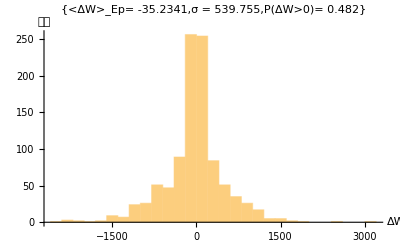

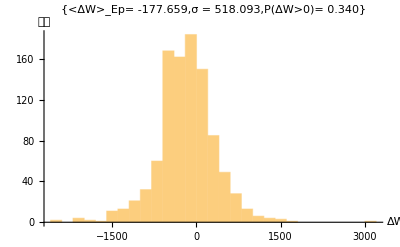

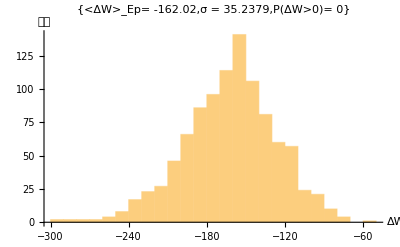

```mathematica
Histogram[W$-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[W$-190]]],"σ = "<>ToString[N[StandardDeviation[W$-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[W$-190]],3]]}]
Histogram[WMG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WMG-190]]],"σ = "<>ToString[N[StandardDeviation[WMG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WMG-190]],3]]}]
Histogram[WBG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WBG-190]]],"σ = "<>ToString[N[StandardDeviation[WBG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WBG-190]],3]]}]
```

```mathematica
Table[N[ActionRecord⟦t,1⟧*A⟦t+1⟧/(√n),2],{t,3,T-1,2}]
```

{-1.3,-3.1,3.9,2.5,0.3,0.9,1.1,-0.9,-2.7,2.3,2.5,-1.3,0.1,0.7,0.9,-1.1,2.9,-1.5,0.3,-1.9,-3.5,-2.5,0.1,-0.7,0.1,0.3,-4.3,3.9,-0.1,-0.1,-0.1,-0.9,-0.1,5.5,-0.1,-0.1,-0.7,-0.3,0.1,-0.9,-1.9,1.9,0.9,-5.7,-2.3,-0.5,-0.1,0.5,-0.7,-5.7,0.1,1.1,-1.7,-1.1,-1.9,5.5,2.1,-2.5,-0.9,-2.1,-0.5,5.5,0.9,2.5,-4.7,1.9,-1.7,-0.5,-0.3,-1.3,-1.1,-1.9,5.5,-5.7,-5.7,1.7,5.5,-0.9,-4.3,3.3,1.1,3.9,-3.3,-3.5,-2.7,2.7,-2.1,4.3,3.5,0.5,-4.1,4.5,4.5,-4.1,-1.7,-2.1,0.5,5.5,-5.7,-2.3,-4.7,-2.5,2.9,2.7,1.1,-3.1,3.3,1.3,3.3,-3.3,-1.5,1.9,1.5,-1.9,-2.9,-2.9,0.7,-4.7,2.5,3.7,2.5,-2.7,-3.7,3.5,1.7,-4.1,0.9,-0.1,2.3,0.5,-0.5,-1.1,-2.3,-0.9,0.1,5.5,-1.3,0.5,-2.1,0.3,-5.7,-5.7,-1.5,0.7,0.5,5.5,2.3,-2.5,0.7,1.1,-3.1,-4.7,-4.1,-3.5,3.9,1.9,-0.5,-0.1,-2.3,3.9,1.9,0.3,1.9,2.1,-2.9,-2.1,-1.1,-3.9,-0.7,-3.9,-1.7,-2.1,0.9,1.9,2.3,3.7,-3.7,-2.1,-1.9,1.7,1.9,-0.5,5.5,2.3,-5.3,0.3,5.5,5.5,-1.7,1.1,0.1,0.1,2.3,5.5,-5.7,-0.3,0.5,5.5}

```mathematica
2/(T-1)Total[UnitStep[Table[ActionRecord⟦t,1⟧*A⟦t+1⟧/(√n),{t,3,T-1,2}]]]//N
```

0.477387

```mathematica
Table[ActionRecord⟦t,1⟧,{t,5,11,2}]
```

{-1,-1,-1,1}

```mathematica
Table[A⟦t+1⟧,{t,5,11,2}]
```

{15,-17,3,-57}

```mathematica
N[Flatten[{c⟦1;;2⟧-100,Total[-ΔcM]},1],5]
N[{9,9,9n}*(Price⟦T⟧-10),5]
N[Flatten[{(NStock⟦1;;2,2⟧-9),-nM⟦T⟧},1]*Price⟦T⟧,5]
```

{-72.2397,463.577,-16191.}

{-51.941,-51.941,-5246.}

{0,-380.59,-245.27}

```mathematica
NStock⟦1;;2,2⟧
```

{9,9}

```mathematica
{W⟦1⟧-190,W⟦2⟧-190,Total[W-190]}
```

{133.733,8.55732,-15123.8}

```mathematica
2170.8+297.3-576.6
```

1891.5

```mathematica
A
N[Total[-ΔcM],4]
N[Table[A⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,0,-7,35,-13,1,-5,1,11}

-200.3

{-65.12,447.5,-149.4,11.59,-55.47,11.19}

```mathematica
nM
N[Price,4]
```

{0,0,0,7,-28,-15,-16,-11,-12}

{10.,10.,10.,9.303,12.79,11.49,11.59,11.09,11.19}

```mathematica
N[Table[-nM⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,74.18,31.94,-329.7,-195.5,-141.}

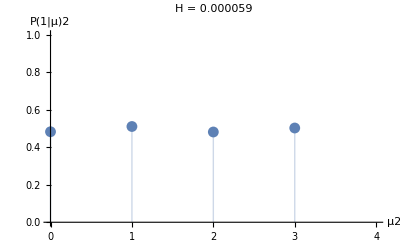

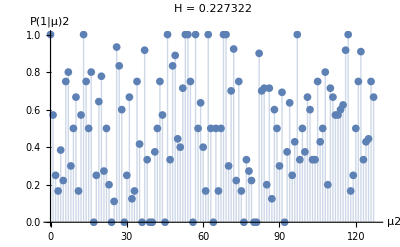

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T/2)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n,2]]]
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

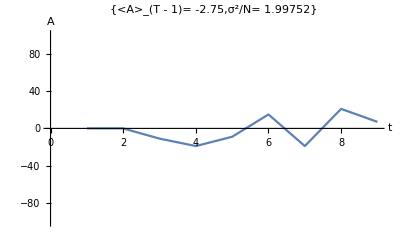

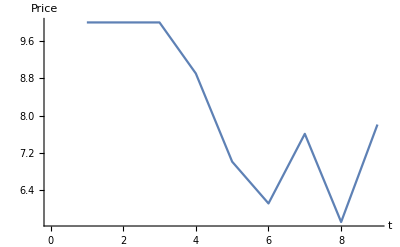

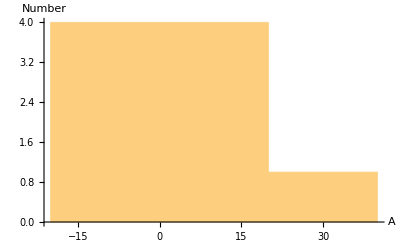

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->{"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]],"σ^2/N= "<>ToString[N[1/n Variance[A]]]}]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

```mathematica
1/(n*T)Sum[(A⟦i⟧)^2,{i,1,n}]//N
```

0.465607

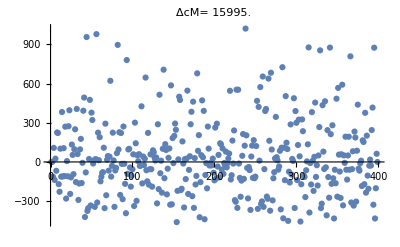

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦1;;T⟧]]]]
```

```mathematica
-Total[ΔcM⟦1;;T⟧]+(9n-nM⟦T⟧)*Price⟦T⟧-(9n*Price⟦1⟧)//N
```

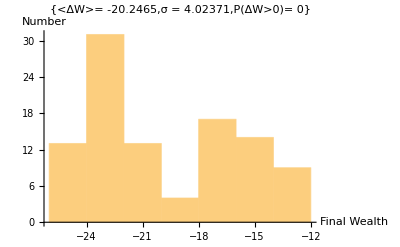

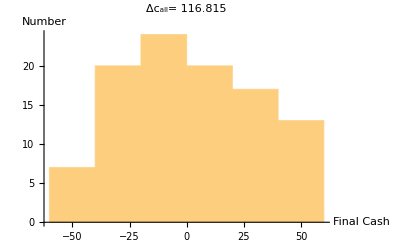

```mathematica
f4=Histogram[W⟦1;;n⟧-190,Automatic,AxesLabel->{"Final Wealth","Number"},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-190]]],"σ = "<>ToString[N[StandardDeviation[W-190]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-190]],3]]}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
{W⟦1⟧-190,W⟦2⟧-190,Total[W-190]}
```

{-18.0102,-23.9804,-2044.9}